```mathematica
n=2; m=4;
µ=(n+m)!/(n!*m!)
SS=Table[Subscript[S, i]=i, {i,0,m}];
t={};
i=1;
Do[If[j+k<m+1, {t=Join[t, {{Subscript[S, j], Subscript[S, k]}}], Subscript[ϕ, i][x_,y_]=x^j*y^k,i=i+1}],{j,0,m}, {k,0,m}]
```

15

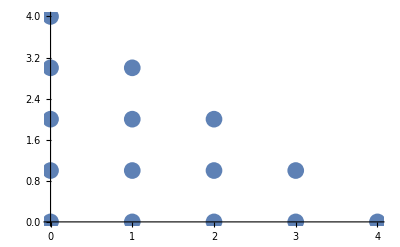

{1,y,y^2,y^3,y^4,x,x y,x y^2,x y^3,x^2,x^2 y,x^2 y^2,x^3,x^3 y,x^4}

```mathematica
ListPlot[t, PlotStyle->PointSize[0.03]]
Table[Subscript[ϕ, i][x,y],{i,1,µ}]
```

```mathematica
V=Table[Subscript[ϕ, j][t[[i,1]],t[[i,2]]],{i,1,µ},{j,1,µ}];
Det[V]≠0
f[x_,y_]=3^(x+y)*Sin[x];
eqv:=Table[∑_(i=1)^µ (Subscript[b, i] Subscript[ϕ, i][t[[k,1]],t[[k,2]]])==f[t[[k,1]],t[[k,2]]],{k,1,µ}]
koef:=Solve[eqv,{}]//Flatten
P[x_,y_]:=∑_(i=1)^µ (Subscript[b, i] Subscript[ϕ, i][x,y])/.koef

P[x,y]//N
```

{1,y,y^2,y^3,y^4,x,x y,x y^2,x y^3,x^2,x^2 y,x^2 y^2,x^3,x^3 y,x^4}

True

5.95219 x-9.05351 x^2+7.1898 x^3-1.56406 x^4-2.0466 x y+13.1676 x^2 y-4.38918 x^3 y-8.18368 x y^2+3.13485 x^2 y^2+3.36588 x y^3

```mathematica
Table[(P[t[[k,1]],t[[k,2]]])==(f[t[[k,1]],t[[k,2]]]),{k,1,µ}]//N
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
mm=Min[SS]; MM=Max[SS];
g1=Plot3D[f[x,y],{x,mm,MM},{y,mm,MM}];
g2=Plot3D[P[x,y],{x,mm,MM},{y,mm,MM}];
Tb1=Table[Point[{t[[i,1]],t[[i,2]],f[t[[i,1]],t[[i,2]]]}],{i,1,µ}];
g3=Graphics3D[{AbsolutePointSize[10],Tb1}];
Show[g1,g2,g3]
```

-Graphics3D-